# Ejemplo de uso de Mathlink

Primero se carga el ejecutable

```mathematica
link = Install[FileNameJoin[{NotebookDirectory[],"bin","FreewayAC_Mathematica"}]]
```

LinkObject[…]

Las funciones diponibles son:

```mathematica
Column@LinkPatterns[link]
```

CreateCircularCA[size_Integer,vmax_Integer,density_Real,randp_Real,initVel_Integer]
CreateOpenCA[size_Integer,vmax_Integer,density_Real,randp_Real,initVel_Integer,newCarProb_Real,newCarSpeed_Integer]
CreateAutonomousCircularCA[size_Integer,vmax_Integer,density_Real,randp_Real,initVel_Integer,autDensity_Real]
CreateAutonomousOpenCA[size_Integer,vmax_Integer,density_Real,randp_Real,initVel_Integer,autDensity_Real,newCarProb_Real,newCarSpeed_Integer]
DeleteCA[]
CAStep[]
CAEvolve[iterations_Integer]
CACountCars[]
CACalculateOcupancy[]
CACalculateFlow[]
CAGetCurrent[]
CAGetHistory[]

Para crear un autómata celular primero hay que generarlo en la memoria del módulo

```mathematica
CreateAutonomousOpenCA[100,5,0.4,0.2,3,0.2,0.5,5]
```

Posteriormente se itera

```mathematica
CAEvolve[100]
```

y por último se cargan los datos a través de las funciones de comunicación: CACalculateOcupancy[], CACalculateFlow[], CAGetCurrent[] y CAGetHistory[]

```mathematica
ca = CAGetHistory[];
```

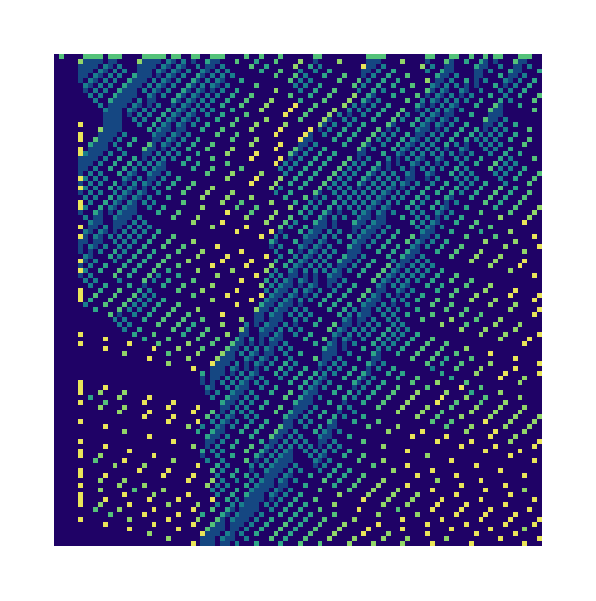

```mathematica
ArrayPlot[ca,ColorFunction->"BlueGreenYellow"]
```

## Animation

```mathematica
CreateCircularCA[100,5,0.4,0.2,3];
CAEvolve[1000];
ca = CAGetHistory[];
```

```mathematica
colorRules = {
-1->White,
0->Black,
1->Blend[{Black,RGBColor[0., 0.25, 0.76]},0.2],
2->Blend[{Black,RGBColor[0., 0.25, 0.76]},0.4],
3->Blend[{Black,RGBColor[0., 0.25, 0.76]},0.6],
4->Blend[{Black,RGBColor[0., 0.25, 0.76]},0.8],
5->Blend[{Black,RGBColor[0., 0.25, 0.76]},1]
};
```

```mathematica
Manipulate[
ArrayPlot[
{ca[[i]]},
ColorFunction->"BlueGreenYellow",
ImageSize->1000,
ColorRules->colorRules
],
{i,1,Length[ca],1}
]
```